```mathematica
Clear["Global`*"];
```

## Sterile neutrino abundance today Ω_s - Dodelson-Widrow Mechanism

#### relativistic degrees of freedom in the plasma

We use the data given in 2005.03544 
[Ken’ichi Saikawa, Satoshi Shirai, 
“Precise WIMP Dark Matter Abundance and Standard Model Thermodynamics”,
JCAP, 2020 (2020)]
(available at https://member.ipmu.jp/satoshi.shirai/DM2020/)
that describe the function shown in Fig.5 in 1803.01038.

```mathematica
(*this comment we can decide to keep, to change or to drop*)
```

```mathematica
gsstab=Import[NotebookDirectory[]<>"/data/gss_Tord.txt", "Table"];
gstarsdata=Table[{gsstab[[i, 1]],gsstab[[i, 2]]} ,{i, 1, Length[gsstab]}];
gs=Interpolation[gstarsdata, InterpolationOrder->2];
```

```mathematica
(*the plots can be omitted in the final version of the code if we think there is no interest in keeping them*)
```

```mathematica
LogLinearPlot[gs[T], {T, 0,10}, PlotLabel->"Entropy relativistic d.o.f.",PlotLegends->{"g_s[T]"}, (*AxesLabel->{"T[GeV]", "g_(*s)"}*) FrameLabel->{Style[HoldForm["T[GeV]"],20,Black,FontFamily->"Times"],Style[HoldForm["g_(*s)"],20,Black,FontFamily->"Times"]}];
```

```mathematica
LogLogPlot[{gs[T], gs'[T]}, {T, 0,10},PlotRange->All, PlotLabel->"Entropy relativistic d.o.f.",PlotLegends->{"g_s[T]", "g_s'[T]"}, (*AxesLabel->{"T[GeV]", "g_(*s)"}*) FrameLabel->{Style[HoldForm["T [GeV]"],20,Black,FontFamily->"Times"],Style[HoldForm[""],20,Black,FontFamily->"Times"]}];
```

#### active neutrinos interaction rate

Interaction rate coefficient for electron neutrinos digitizing Fig. 1 in 1512.05369 
[Alexander Merle, Aurel Schneider, Maximilian Totzauer, 
“Dodelson-Widrow production of sterile neutrino Dark Matter with non-trivial initial abundance”, 
JCAP, 04, 003 (2016)]

```mathematica
Cedata = Import[NotebookDirectory[]<>"/data/C_e.txt", "Table"];
Ce=Interpolation[Cedata, InterpolationOrder->1];
```

```mathematica
(*the plot can be omitted in the final version of the code if we think there is no interest in keeping it*)
```

```mathematica
LogLinearPlot[Ce[T], {T, 0,10}, PlotLabel->"Interaction rate coefficient C_e", (*AxesLabel->{"T[GeV]", "C_e"}*) FrameLabel->{Style[HoldForm["T [GeV]"],20,Black,FontFamily->"Times"],Style[HoldForm["C_e"],20,Black,FontFamily->"Times"]}];
```

#### sterile neutrinos and antineutrinos distribution functions

```mathematica
fνs=Function[{r,sin22θ,ms,Ti,Tf}, Block[{ηB= 6.05*10^−10,
GF=1.166*10^-5,
MPl=1.22* 10^19,
mZ= 91.1876,
mW= 80.379 (*last 4 quantities in GeV*)},{$MaxExtraPrecision=1000};
NIntegrate[- Sqrt[90/(8 π^3*gs[T])] MPl/T^3(1+T/3(gs'[T]/gs[T]))*(Ce[T]/4 GF^2 T^4*(gs[T]/gs[Tf])^(1/3) r *T)*
(ms^2/(2 ((gs[T]/gs[Tf])^(1/3)r*T)))^2*sin22θ/ ((ms^2/(2 ((gs[T]/gs[Tf])^(1/3)r*T)))^2*sin22θ+ 
(Ce[T] GF^2 T^4*(gs[T]/gs[Tf])^(1/3) r *T)^2/4 + 
(ms^2/(2 ((gs[T]/gs[Tf])^(1/3)r*T))- (Sqrt[2] *GF*2*Zeta[3]*T^3*ηB)/(4*π^2) + (8*Sqrt[2]*GF)/(3 mZ^2)*(gs[T]/gs[Tf])^(1/3)*r*T*2*3/4 Zeta[3]/π^2 T^3*7/180 π^4/Zeta[3] T + (8*Sqrt[2]*GF)/(3 mW^2)*(gs[T]/gs[Tf])^(1/3)*r*T*2*2/(2 π^2)T^3*5.6822*T)^2)*
(Exp[(gs[T]/gs[Tf])^(1/3)r]+1)^-1,{T,Ti,Tf},
Method->{"AdaptiveQuasiMonteCarlo","MaxPoints"->10^9},MaxRecursion->20]]];
```

```mathematica
fantiνs= Function[{r,sin22θ,ms,Ti,Tf}, Block[{GF=1.166*10^-5,
MPl=1.22* 10^19,
ηB= 6.05*10^−10,
mZ= 91.1876,
mW= 80.379 (*last 4 quantities in GeV*)},
{$MaxExtraPrecision=1000};
NIntegrate[- Sqrt[90/(8 π^3*gs[T])] MPl/T^3(1+T/3(gs'[T]/gs[T]))*(Ce[T]/4 GF^2 T^4*(gs[T]/gs[Tf])^(1/3) r *T)*
(ms^2/(2 ((gs[T]/gs[Tf])^(1/3)r*T)))^2*sin22θ/ ((ms^2/(2 ((gs[T]/gs[Tf])^(1/3)r*T)))^2*sin22θ+ 
(Ce[T] GF^2 T^4*(gs[T]/gs[Tf])^(1/3) r *T)^2/4 + 
(ms^2/(2 ((gs[T]/gs[Tf])^(1/3)r*T))+ (Sqrt[2] *GF*2*Zeta[3]*T^3*ηB)/(4*π^2) + (8*Sqrt[2]*GF)/(3 mZ^2)*(gs[T]/gs[Tf])^(1/3)*r*T*2*3/4 Zeta[3]/π^2 T^3*7/180 π^4/Zeta[3] T + (8*Sqrt[2]*GF)/(3 mW^2)*(gs[T]/gs[Tf])^(1/3)*r*T*2*2/(2 π^2)T^3*5.6822*T)^2)*
(Exp[(gs[T]/gs[Tf])^(1/3)r]+1)^-1,{T,Ti,Tf},
Method->{"AdaptiveQuasiMonteCarlo","MaxPoints"->10^9},MaxRecursion->20]]];
```

#### sterile neutrino dark matter relic density

```mathematica
ΩDW =Function[{sin22θ,ms,Ti,Tf},
Block[{s0=2891.2 (*cm^-3*), 
ρc= 1.054*10^-5 (*(GeV/c^2)cm^-3*)},
psdnu=Interpolation[Log[Table[{10^n,fνs[10^n,sin22θ,ms,Ti,Tf]},{n,-3,2,0.1}]],Method->"Hermite"];(*interpolated after changing to log scale for better fit*)
f[r_]:=Exp[psdnu[Log[r]]];
psdnubar=Interpolation[Log[Table[{10^n,fantiνs[10^n,sin22θ,ms,Ti,Tf]},{n,-3,2,0.1}]],Method->"Hermite"];(*interpolated after changing to log scale for better fit*)
fbar[r_]:=Exp[psdnubar[Log[r]]];
s0/ρc*45/(4 π^4*10.75)*ms*
NIntegrate[(f[r]+fbar[r])*r^2,{r,0.,500.},
Method->{"AdaptiveQuasiMonteCarlo","MaxPoints"->10^9},MaxRecursion->30]]];
```

```mathematica
ΩDW[10*10^-11,1*10^-6,1,0.002]//AbsoluteTiming
```

{3.36649,0.000177795}

```mathematica
(* masses Subscript[m, s] in the range [1, 100] keV*)
ms=Table[10^n,{n,-6,-4,0.4}];
(*sin^2 2θ in the range [10^-10, 10^-4] *)
sin22θ=Table[10^n,{n,-10,-4,0.25}];
(*creating a paired list of all possible mass and mixing angles generated above *)
variables=Tuples[{sin22θ,ms}];
```

```mathematica
time=AbsoluteTime[];
```

```mathematica
(* creates a list {{sin^2(2θ), Subscript[m, s]}, Subscript[Ω, DW][sin^2(2θ), Subscript[m, s]]} for Ti=1 GeV and Tf=0.002 GeV*)
OmegaDW=Map[{{#[[1]],#[[2]]},ΩDW[#[[1]],#[[2]],1.,0.002]}& , variables];
```

```mathematica
(*Interpolating the list of abundance values to get a smoother plot *)
ΩSDW=Interpolation[OmegaDW, InterpolationOrder->2];
```

```mathematica
(*collecting all the values of sin^2(2θ) and Subscript[m, s] such that Subscript[Ω, s] h^2=0.12 for dw-produced sterile neutrinos*)plsDW=Normal@ContourPlot[{ΩSDW[sin22θ,ms ]==0.12}, {sin22θ, 10^-14, 10^-4},{ms, 10^-6, 10^-4},PlotPoints->800];
```

```mathematica
(*expressing mass values in keV (rather than GeV) and rescaling cases{sin^2(2θ), Subscript[m, s]} to log scale *)
LinelistDW=Cases[ plsDW,Line[a_,b___]:>a,Infinity]⟦1⟧;
LinelistDWr=Table[{LinelistDW⟦i,1⟧,LinelistDW⟦i,2⟧*10^6} ,{i,1,Length[LinelistDW]}];
LinelistDWlog =  Table[{Log10[LinelistDWr⟦i,1⟧], Log10[LinelistDWr⟦i,2⟧]}, {i ,1,Length[LinelistDWr]}];
```

```mathematica
AbsoluteTime[]-time
```

476.976165

### results (comparison) plot

#### Plot settings

```mathematica
Import[NotebookDirectory[] <>"/tools/LogScale.m"];
Import[NotebookDirectory[] <>"/tools/LogTicks.m"];
Import[NotebookDirectory[] <>"/tools/MyGrid.m"];
Import[NotebookDirectory[] <>"/tools/KPTools.m"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
ticksx=LogTicks[-15, -2,2];
ticksy=LogTicks[0,2,1];
ticksx0=LogTicksNoLabel[-14,-2];
ticksy0=LogTicksNoLabel[0,2];
ticksy= {{0.,"1"},{1.,"10"},{2.,"100"},{0.30102999566398114,"",{0.00375,0.},{Thickness[0.001]}},{0.47712125471966244,"",{0.00375,0.},{Thickness[0.001]}},{0.6020599913279623,"",{0.00375,0.},{Thickness[0.001]}},{0.6989700043360187,"",{0.00375,0.},{Thickness[0.001]}},{0.7781512503836435,"",{0.00375,0.},{Thickness[0.001]}},{0.8450980400142567,"",{0.00375,0.},{Thickness[0.001]}},{0.9030899869919434,"",{0.00375,0.},{Thickness[0.001]}},{0.9542425094393249,"",{0.00375,0.},{Thickness[0.001]}},{1.301029995663981,"",{0.00375,0.},{Thickness[0.001]}},{1.4771212547196624,"",{0.00375,0.},{Thickness[0.001]}},{1.6020599913279623,"",{0.00375,0.},{Thickness[0.001]}},{1.6989700043360185,"",{0.00375,0.},{Thickness[0.001]}},{1.7781512503836434,"",{0.00375,0.},{Thickness[0.001]}},{1.845098040014257,"",{0.00375,0.},{Thickness[0.001]}},{1.9030899869919433,"",{0.00375,0.},{Thickness[0.001]}},{1.9542425094393248,"",{0.00375,0.},{Thickness[0.001]}}};
```

#### DM lifetime constraint

(A comment on the origin of this constraint is still missing here or in the .pdf file containing more details and explanations - I can write some lines about that later)

```mathematica
mainchannelbound={10^#,(267/10^#)^(1/5)}&/@Table[i,{i,-14,-1,0.1}];
mainchannelbound= Table[{mainchannelbound[[i,1]],mainchannelbound[[i,2]]} ,{i,1,Length[mainchannelbound]}];
mainchannelbound= Join[{{10^3,First[mainchannelbound][[2]]}},mainchannelbound,{{10^3,Last[mainchannelbound][[2]]}}];
mainchannelboundlog =  Table[{Log10[mainchannelbound[[i,1]]], Log10[mainchannelbound[[i,2]]]}, {i ,1,Length[mainchannelbound]}];
```

#### KATRIN sensitivity

KATRIN statistical sensitivity with 3 years of data,
taken from 1810.06711
[KATRIN Collaboration, S. Mertens et al., 
“A novel detector system for KATRIN to search for keV-scale sterile neutrinos”,  
J. Phys. G: Nucl. Part. Phys. 46 065203 (2019)]

```mathematica
Kstat=Import[NotebookDirectory[]<>"/data/KATstat.txt", "Table"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ)*)
```

```mathematica
Kstatres= Table[{Kstat[[i,1]],Kstat[[i,2]]*4} ,{i,1,Length[Kstat]}];
```

```mathematica
(*rescaled data in the inverted order*)
```

```mathematica
KATstatI=Transpose[{Table[Kstatres[[i,2]],{i,1,Length[Kstatres]}],Table[Kstatres[[i,1]],{i,1,Length[Kstatres]}]}];
KATstatI= Join[{{10^3,First[KATstatI][[2]]}},KATstatI,{{10^3,Last[KATstatI][[2]]}}];
KATstatIr = Table[{KATstatI[[i,1]],KATstatI[[i,2]]*10^6} ,{i,1,Length[KATstatI]}];
KATstatIlog =  Table[{Log10[KATstatIr[[i,1]]], Log10[KATstatIr[[i,2]]]}, {i ,1,Length[KATstatIr]}];
```

#### Final plot

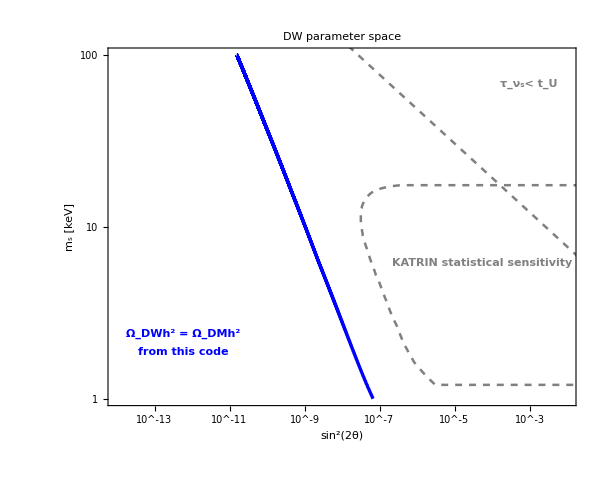

```mathematica
parameterspaceDW=Plot[{},{x,-16,-3},PlotRange->{{-14, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],20,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],20,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, PlotLabel->Row[{
"DW parameter space"}],
Prolog->{
(*Red,Thick,Thickness[0.004],Line[parameterspace160107553],
Hue[0.84,1,1],Thick,Thickness[0.004],Line[parameterspace160900667],
Hue[0.5,0.79,0.88],Thick,Thickness[0.004],Line[parameterspace170502184],
Hue[0.22,1,0.5],Thick,Thickness[0.004],Line[parameterspace170602707],
Green,Thick,Thickness[0.004],Line[parameterspace190308296],
Orange,Thick,Thickness[0.004],Line[parameterspace191004901] ,
Brown,Thick,Thickness[0.004],Line[parameterspace191100328],
Hue[0.15,1,0.99],Thick,Thickness[0.004],Line[parameterspace200503039],*)
Blue,Thick,Thickness[0.004],Line[LinelistDWlog],
(*Darker[Blue],Thick,Thickness[0.004],Line[LinelistDWnotlog],*)
Gray,Dashed,Thickness[0.003],Line[KATstatIlog],
Gray,Dashed,Thickness[0.003],Line[mainchannelboundlog]
 },

Epilog->{FontSize->15,
Blue, Text[Rotate[Style["Ω_DWh^2 = Ω_DMh^2",Bold],-0 Degree,Bold],Scaled[{0.16,0.2}]],
(*FontSize->12,
Red, Text[Rotate[Style["from 1601.07553"],-0 Degree],Scaled[{0.16,0.65}]],
Hue[0.5,0.79,0.88], Text[Rotate[Style["from 1705.02184"],-0 Degree],Scaled[{0.16,0.6}]],
Hue[0.22,1,0.5], Text[Rotate[Style["from 1706.02707"],-0 Degree],Scaled[{0.16,0.55}]],
Brown, Text[Rotate[Style["from 1911.00328"],-0 Degree],Scaled[{0.16,0.5}]],
Green, Text[Rotate[Style["from 1903.08296"],-0 Degree],Scaled[{0.16,0.45}]],
Orange, Text[Rotate[Style["from 1910.04901", Bold],-0 Degree],Scaled[{0.16,0.4}]],
Hue[0.84,1,1], Text[Rotate[Style["from 1609.00667", Bold],-0 Degree],Scaled[{0.16,0.35}]],
Hue[0.15,1,0.99], Text[Rotate[Style["from 2005.03039", Bold],-0 Degree],Scaled[{0.16,0.3}]],*)
FontSize->15,
Blue, Text[Rotate[Style["from this code", Bold],-0 Degree],Scaled[{0.16,0.15}]],
FontSize->15,
Gray, Text[Rotate[Style["KATRIN statistical sensitivity", Bold],-0 Degree],Scaled[{0.8,0.4}]],
FontSize->20,
Gray, Text[Rotate[Style["τ_ν_s< t_U", Bold],-0 Degree],Scaled[{0.9,0.9}]]},

FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}}]
```

## comparison with other results

#### lines from other papers

Sterile neutrino relic abundance parameter space plot from 1601.07553 Fig .1

```mathematica
parameterspace160107553= Import[NotebookDirectory[]<>"/data/parameter_space_1601-07553.txt", "Table"];
parameterspace160107553={Last@#,First@#}&/@ parameterspace160107553;
parameterspace160107553 =  Table[{Log10[parameterspace160107553[[i,1]]], Log10[parameterspace160107553[[i,2]]]}, {i ,1,Length[parameterspace160107553]}];
```

Sterile neutrino relic abundance parameter space plot from 1609.00667 Fig .1

```mathematica
parameterspace160900667= Import[NotebookDirectory[]<>"/data/parameter_space_1609-00667.txt", "Table"];(*already in log scale*)
parameterspace160900667={Last@#,First@#}&/@ parameterspace160900667;
```

Sterile neutrino relic abundance parameter space plot from 1705.02184 Fig .3

```mathematica
parameterspace170502184= Import[NotebookDirectory[]<>"/data/parameter_space_1705-02184.txt", "Table"];(*already in log scale*)
parameterspace170502184={Last@#,First@#}&/@ parameterspace170502184;
```

Sterile neutrino relic abundance parameter space plot from 1706.02707 Fig .2

```mathematica
parameterspace170602707= Import[NotebookDirectory[]<>"/data/parameter_space_1706-02707.txt", "Table"];(*already in log scale*)
parameterspace170602707={Last@#,First@#}&/@ parameterspace170602707;
```

Sterile neutrino relic abundance parameter space plot from 1903.08296 Fig .1

```mathematica
parameterspace190308296= Import[NotebookDirectory[]<>"/data/parameter_space_1903-08296.txt", "Table"];(*already in log scale*)
parameterspace190308296={Last@#,First@#}&/@ parameterspace190308296;
```

Sterile neutrino relic abundance parameter space plot from 1910.04901 Fig .5

```mathematica
parameterspace191004901= Import[NotebookDirectory[]<>"/data/parameter_space_1910-04901.txt", "Table"];(*already in log scale*)
parameterspace191004901={Last@#,First@#}&/@ parameterspace191004901;
```

Sterile neutrino relic abundance parameter space plot from 1911.00328 Fig .2a

```mathematica
parameterspace191100328= Import[NotebookDirectory[]<>"/data/parameter_space_1911-00328.txt", "Table"];(*already in log scale*)
```

Sterile neutrino relic abundance parameter space plot from 2005.03039 Fig .4

```mathematica
parameterspace200503039= Import[NotebookDirectory[]<>"/data/parameter_space_2005-03039.txt", "Table"];
parameterspace200503039={Last@#,First@#}&/@ parameterspace200503039;
parameterspace200503039 =  Table[{Log10[parameterspace200503039[[i,1]]], Log10[parameterspace200503039[[i,2]]]}, {i ,1,Length[parameterspace200503039]}];
```

#### line from sterile-dm (to be obtained)

(If the problem of the redshift of momenta does not get solved I will tell you how to get this line without wasting too much time in that)

#### Final plot with comparison with other sources and different bounds

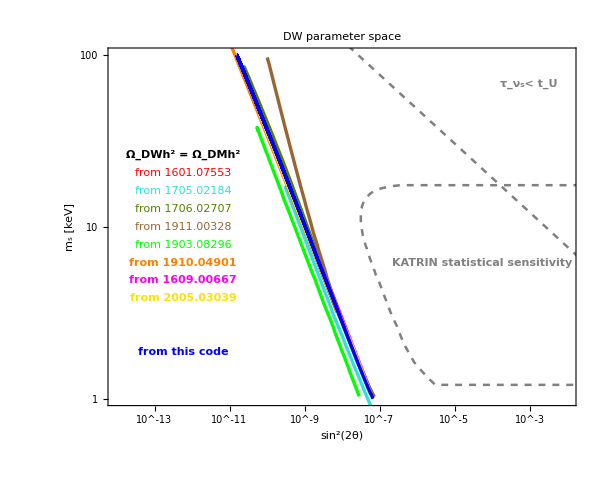

```mathematica
parameterspace=Plot[{},{x,-16,-3},PlotRange->{{-14, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],20,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],20,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, PlotLabel->Row[{
"DW parameter space"}],
Prolog->{
Red,Thick,Thickness[0.004],Line[parameterspace160107553],
Hue[0.84,1,1],Thick,Thickness[0.004],Line[parameterspace160900667],
Hue[0.5,0.79,0.88],Thick,Thickness[0.004],Line[parameterspace170502184],
Hue[0.22,1,0.5],Thick,Thickness[0.004],Line[parameterspace170602707],
Green,Thick,Thickness[0.004],Line[parameterspace190308296],
Orange,Thick,Thickness[0.004],Line[parameterspace191004901] ,
Brown,Thick,Thickness[0.004],Line[parameterspace191100328],
Hue[0.15,1,0.99],Thick,Thickness[0.004],Line[parameterspace200503039],
(*Brown,Thick,Thickness[0.004],Line[parameterspace],*)
Blue,Thick,Thickness[0.004],Line[LinelistDWlog],
(*Darker[Blue],Thick,Thickness[0.004],Line[LinelistDWnotlog],*)
Gray,Dashed,Thickness[0.003],Line[KATstatIlog],
Gray,Dashed,Thickness[0.003],Line[mainchannelboundlog]
 },

Epilog->{FontSize->20,
Black, Text[Rotate[Style["Ω_DWh^2 = Ω_DMh^2",Bold],-0 Degree,Bold],Scaled[{0.16,0.7}]],
FontSize->12,
Red, Text[Rotate[Style["from 1601.07553"],-0 Degree],Scaled[{0.16,0.65}]],
Hue[0.5,0.79,0.88], Text[Rotate[Style["from 1705.02184"],-0 Degree],Scaled[{0.16,0.6}]],
Hue[0.22,1,0.5], Text[Rotate[Style["from 1706.02707"],-0 Degree],Scaled[{0.16,0.55}]],
Brown, Text[Rotate[Style["from 1911.00328"],-0 Degree],Scaled[{0.16,0.5}]],
Green, Text[Rotate[Style["from 1903.08296"],-0 Degree],Scaled[{0.16,0.45}]],
Orange, Text[Rotate[Style["from 1910.04901", Bold],-0 Degree],Scaled[{0.16,0.4}]],
Hue[0.84,1,1], Text[Rotate[Style["from 1609.00667", Bold],-0 Degree],Scaled[{0.16,0.35}]],
Hue[0.15,1,0.99], Text[Rotate[Style["from 2005.03039", Bold],-0 Degree],Scaled[{0.16,0.3}]],
FontSize->15,
Blue, Text[Rotate[Style["from this code", Bold],-0 Degree],Scaled[{0.16,0.15}]],
(*Darker[Blue], Text[Rotate[Style["from this code - no int.", Bold],-0 Degree],Scaled[{0.16,0.1}]],*)
FontSize->15,
Gray, Text[Rotate[Style["KATRIN statistical sensitivity", Bold],-0 Degree],Scaled[{0.8,0.4}]],
FontSize->20,
Gray, Text[Rotate[Style["τ_ν_s< t_U", Bold],-0 Degree],Scaled[{0.9,0.9}]]},

FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}}]
```